## LieARTCharacters

### Setup

```mathematica
SetDirectory@NotebookDirectory[];
<<LieARTCharacters`
```

```mathematica
PacletUninstall/@PacletFind["LieARTC*"]
PacletInstall["/Users/jose/Developer/LieARTCharacters/build/LieARTCharacters-2.1.0.paclet",ForceVersionInstall->True]
```

```mathematica
ClearAll[generateLogo];
generateLogo[algebra_:LieART`E6,thick_:0.005,opa_:0.8]:=
Module[{delta,eig,roots,grouped,ig,jg,xx,yy,eg,ln,gp,normK,colorFn,d},
delta=List@@@OrthogonalSimpleRoots[algebra];
eig=Simplify@ToRadicals@Eigenvectors[CartanMatrix[algebra]]//Last;
roots=RootSystem[algebra]//OrthogonalBasis//MapApply[List];
grouped=AssociationThread[Range[Length@delta],delta];
{ig,jg}=FindGraphPartition@RelationGraph[
Dot[Lookup[grouped,#1],Lookup[grouped,#2]]==0&,
Keys[grouped]
];
xx=Total[eig[[ig]]delta[[ig]]]//N;
yy=Total[eig[[jg]]  delta[[jg]]]//N;
xx=Normalize[xx];
yy=yy-Dot[xx,yy]xx;
yy=Normalize[yy];
eg=UndirectedEdge@@@Select[Subsets[roots,{2}],Dot[{1,-1} . #,{1,-1} . #]==4&];
ln=MapAt[{# . xx,# . yy}&,Line@*List@@@eg,{All,1,All}];
d=Chop@TransformedRegion[BoundingRegion[Map[{# . xx,# . yy}&,roots],"MinDisk"],1.1#&];
colorFn[l_]:=Max[Norm/@Identity@@l];
ln=ReverseSortBy[RegionMeasure]@Select[ln,
And[Not@PossibleZeroQ@Chop@colorFn[#],Not@PossibleZeroQ@RegionMeasure@#]&
];
gp=Map[colorFn,ln];
normK[x_]=0.001+0.998((x-Min@gp)/(Max@gp-Min@gp));
Graphics[{
{DropShadowing[{0,0},5],FaceForm[White],d},
Map[{ColorData["Rainbow"][0.05+0.75normK[colorFn@#1]],Thickness[thick],Opacity[opa],#1}&,ln]
},
PlotRangePadding->Scaled[.05],
ImageSize->{128,128}
]
]
Export["logo.svg",Echo@generateLogo[E6,0.005,0.8],ImageSize->{64,64}]
```

-Graphics-

logo.svg

```mathematica
generateLogo[E6,0.005,0.8]
```

-Graphics-

```mathematica
BoundingRegion
```

```mathematica
BoundingRegion@First@generateLogo[E6,0.005,0.8]
```

### LieART extension/modding

#### Rank

Rank now works with ProductAlgebra, ProductIrrep and ProductWeight, returning the rank of the underlying algebra.

```mathematica
Rank@ProductAlgebra[A2,A2,A2]
```

6

```mathematica
Rank@ProductWeight[Weight[A2][1,0],Weight[A2][1,1],Weight[A2][1,2]]
```

6

#### Algebra

Algebra gives the correct result for ProductIrrep, ProductWeight, IrrepPlus and IrrepTimes returning the algebra we are working with.

```mathematica
Algebra@ProductIrrep[Irrep[A1][1],Irrep[D2][1,0],Irrep[B2][1,1]]
```

A_1×D_2×B_2

```mathematica
IrrepPlus[
ProductIrrep[Irrep[A2][1,0],Irrep[A2][1,0],Irrep[A2][0,1]],
IrrepTimes[3,ProductIrrep[Irrep[A2][0,1],Irrep[A2][1,0],Irrep[A2][0,1]]]
]
%//Algebra
```

((10),(10),(01))+3((01),(10),(01))

A_2×A_2×A_2

```mathematica
Algebra@IrrepPlus[Irrep[D2][1,0],Irrep[A2][0,1]]
```

Algebra::irrplusdiff: IrrepPlus contains irreps of different algebras {A_2,D_2}.

Algebra[(10)+(01)]

#### Irrep / ProductIrrep and Weight / Product Weight

Irrep/Weight of ProductAlgebra automatically expands to ProductIrrep/ProductWeight.

```mathematica
Irrep[ProductAlgebra[A1,A2,A1]][1,1,0,2]
%//FullForm
```

((1),(10),(2))

ProductIrrep[Irrep[A][1],Irrep[A][1,0],Irrep[A][2]]

#### WeylDimensionFormula

```mathematica
WeylDimensionFormula[ProductAlgebra[A2,A2,A2]][x1,x2,y1,y2,z1,z2]
WeylDimensionFormula[A2][x1,x2]WeylDimensionFormula[A2][y1,y2]WeylDimensionFormula[A2][z1,z2]
%==%%
```

1/8 (1+x1) (1+x2) (2+x1+x2) (1+y1) (1+y2) (2+y1+y2) (1+z1) (1+z2) (2+z1+z2)

1/8 (1+x1) (1+x2) (2+x1+x2) (1+y1) (1+y2) (2+y1+y2) (1+z1) (1+z2) (2+z1+z2)

True

### Computation of characters

χ[irrep] computes the “pure function” using WeightSystem[irrep] of LieART and saves it in the current session memory since the computation of the weights can be time consuming.
The variable $SaveCharacterDefinitions can be modified if memory is a concern.

```mathematica
χ[Irrep[E6][1,0,0,0,0,0]]
```

χ[(100000)]

```mathematica
χ[Irrep[E6][1,0,0,0,0,0]][z1,z2,z3,z4,z5,z6]
```

χ[(100000)][z1,z2,z3,z4,z5,z6]

By default, Algebra[A][n] algebra family is used if a list of Dynkin labels is provided.

```mathematica
χ[{1,0,0}]
```

χ[{1,0,0}]

There are different ways of calling χ. Additionally, ProductAlgebra also is compatible.

```mathematica
χ[E6,{1,0,0,0,0,0}]==χ[Irrep[E6][1,0,0,0,0,0]]
```

χ[E_6,{1,0,0,0,0,0}]==χ[(100000)]

```mathematica
χ[ProductAlgebra[A2,B2,C2],{{1,0},{0,1},{1,1}}]==χ[ProductIrrep[Irrep[A][1,0],Irrep[B][0,1],Irrep[C][1,1]]]==χ[{A2,B2,C2},{{1,0},{0,1},{1,1}}]
```

χ[A_2×B_2×C_2,{{1,0},{0,1},{1,1}}]==χ[((10),(01),(11))]==χ[{A_2,B_2,C_2},{{1,0},{0,1},{1,1}}]

More importantly, IrrepPlus and IrrepTimes automatically expand and give the correct result in terms of character sum and multiplication.

```mathematica
χ[IrrepPlus[
ProductIrrep[Irrep[A2][1,0],Irrep[A2][1,0],Irrep[A2][0,1]],
IrrepTimes[3,ProductIrrep[Irrep[A2][0,1],Irrep[A2][1,0],Irrep[A2][0,1]]]
]]
```

χ[((10),(10),(01))+3((01),(10),(01))]

### Character sum decomposition

Assume a random ansatz for a product algebra of three A_2 algebras

```mathematica
g=ProductAlgebra[A2,A2,A2];
irrepSampleList=RandomInteger[{0,3},{8,Rank[g]}]
irrepList=Irrep[g]@@@irrepSampleList
```

{{1,1,0,1,2,2},{0,2,3,1,1,2},{3,0,1,1,2,1},{3,2,2,1,1,2},{3,0,2,0,0,3},{0,0,0,3,1,1},{0,0,3,2,2,3},{3,1,0,1,3,1}}

{((11),(01),(22)),((02),(31),(12)),((30),(11),(21)),((32),(21),(12)),((30),(20),(03)),((00),(03),(11)),((00),(32),(23)),((31),(01),(31))}

```mathematica
irrepAnsatz=IrrepPlus@@MapIndexed[
Function[{rep,i},IrrepTimes[a[First@i],rep]],
irrepList
]
```

a[1]((11),(01),(22))+a[2]((02),(31),(12))+a[3]((30),(11),(21))+a[4]((32),(21),(12))+a[5]((30),(20),(03))+a[6]((00),(03),(11))+a[7]((00),(32),(23))+a[8]((31),(01),(31))

```mathematica
ansatz=Expand[
Ch[irrepAnsatz][z1,z2,z3,z4,z5,z6]
]
```

```mathematica
decomp=CharacterDecomposition[g][ansatz,{z1,z2,z3,z4,z5,z6}]
```

<|((00),(00),(00))→χ[a[1]((03),(10),(12))+a[2]((12),(21),(23))+a[3]((02),(21),(30))+a[4]((01),(21),(30))+a[5]((23),(12),(30))+a[6]((01),(03),(01))+a[7]((11),(33),(33))+a[8]((32),(13),(33))][z1,z2,z3,z4,z5,z6]|>

```mathematica
Total@KeyValueMap[#2 χ[#1][z1,z2,z3,z4,z5,z6]&,decomp]-ansatz//ExpandAll
```

-χ[a[1]((03),(10),(12))+a[2]((12),(21),(23))+a[3]((02),(21),(30))+a[4]((01),(21),(30))+a[5]((23),(12),(30))+a[6]((01),(03),(01))+a[7]((11),(33),(33))+a[8]((32),(13),(33))][z1,z2,z3,z4,z5,z6]+χ[a[1]((03),(10),(12))+a[2]((12),(21),(23))+a[3]((02),(21),(30))+a[4]((01),(21),(30))+a[5]((23),(12),(30))+a[6]((01),(03),(01))+a[7]((11),(33),(33))+a[8]((32),(13),(33))][z1,z2,z3,z4,z5,z6] χ[((00),(00),(00))][z1,z2,z3,z4,z5,z6]

### Highest weights

For the computation of the decomposition it is necessary to order the dominant weights and extract the highest weights from a given expression.

```mathematica
g=B3;
irrepSampleList=RandomInteger[{0,2},{3,Rank[g]}]
irrepList=Irrep[g]@@@irrepSampleList;
weightList=Flatten[WeightSystem/@irrepList];
```

{{2,2,0},{2,1,2},{0,2,1}}

The highest weights can be computed as the  root nodes of a relation graph. We compute the well-known weak ordering using DominantWeightOrder

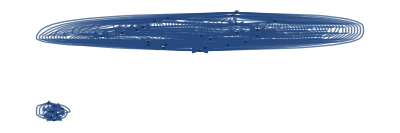

```mathematica
RelationGraph[DominantWeightOrder[#1,#2]>0 &,Union@DominantWeights@weightList]
```

For a list of weights we use HighestWeights

```mathematica
HighestWeights[weightList]
```

{(2, 1, 2),(0, 2, 1)}

For an expression which is given by a sum of characters we can use HighestWeightsFrom

```mathematica
testCharacter=Sum[χ[ir][z1,z2,z3],{ir,irrepList}];
```

```mathematica
HighestWeightsFrom[g][testCharacter,{z1,z2,z3}]
```

{(0, 0, 0)}